# Image analysis of experimental results

## Data reading

### read in a single tiff

```mathematica
(*filename="data/Series017.tif";
SetDirectory[NotebookDirectory[]];*)
```

```mathematica
(*rawim=Import[filename];*)
```

```mathematica
(*timeunit=0.0852;
pixelunit=0.159688;
velocityunit=pixelunit/timeunit;*)
```

```mathematica
(*filecount=Length@rawim;*)
```

```mathematica
(*dims=ImageDimensions[rawim[[1]]];*)
```

### read in a batch of tiffs

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
timeunit=0.0852;
pixelunit=0.159688;
velocityunit=pixelunit/timeunit;
```

```mathematica
directory = "data";
```

```mathematica
filecount=400;
```

```mathematica
Monitor[rawim=Table[Import[directory<>"/t"<>IntegerString[i,10,3]<>".tif"],{i,0,filecount-1}];,i]
```

```mathematica
dims=ImageDimensions[rawim[[1]]];
```

## Manual Contrast Setting

```mathematica
lims=Mean[ImageMeasurements[rawim,{"Min","Max"}]];
```

```mathematica
aim=(ImageAdjust[#,{0,0,1},{0.005,0.02}]&/@rawim);
```

```mathematica
daim=(ImageData/@aim);
```

## Particle tracking

### Grid of images

#### Grid calculation

Calculate space grids:

```mathematica
disc=8;
gridcorners=Table[{(x-1)*dims[[1]]/disc,(y-1)*dims[[2]]/disc},{x,1,disc+1},{y,1,disc+1}];
gridmiddles=Table[{(x-0.5)*dims[[1]]/disc,(y-0.5)*dims[[2]]/disc},{x,1,disc},{y,1,disc}];
```

```mathematica
igrid=Table[(ImageTake[#,{gridcorners[[x,y,2]],gridcorners[[x,y+1,2]]},{gridcorners[[x,y,1]],gridcorners[[x+1,y,1]]}]&/@aim),{x,1,disc},{y,1,disc}];
```

```mathematica
igrid//TensorDimensions
```

{8,8,400}

Calculate density grids:

```mathematica
densitygrid=Table[Table[Flatten[
mean=(daim[[t,((dims[[2]]/disc)*(y-1)+1);;(y*dims[[2]]/disc),((dims[[1]]/disc)*(x-1)+1);;(x*dims[[1]]/disc)]]//Flatten//Mean);
{gridmiddles[[x,y]],mean}],{x,1,disc},{y,1,disc}],{t,1,filecount-1}];
densitygrid[[;;,;;,;;,2]]=dims[[2]]-densitygrid[[;;,;;,;;,2]];
```

Calculate velocity grids: (Note that the function ImageFeatureTrack operates according to the Kanade-Lucas-Tomasi feature tracking method)

```mathematica
Monitor[allvelos=Table[
points=Table[ImageFeatureTrack[igrid[[x,y,i;;i+1]],MaxFeatureDisplacement->1],{i,1,filecount-1}];
pointscorrected=Table[Delete[#,Position[points[[i,2]],_Missing]]&/@points[[i]],{i,1,filecount-1}];
Replace[(Flatten[Differences/@pointscorrected,1]),{}->{{0,0}},1]
,{x,1,disc},{y,1,disc}];,x]

velogrid=Table[({gridmiddles[[x,y]],Total[#]}&/@allvelos[[x,y]])
,{x,1,disc},{y,1,disc}];
velogrid[[;;,;;,;;,1,2]]=dims[[2]]-velogrid[[;;,;;,;;,1,2]];
```

```mathematica
veloampgrid=velogrid;
veloampgrid[[;;,;;,;;,2]]=Table[Norm[veloampgrid[[x,y,t,2]]]*densitygrid[[t,x,y,3]],{x,1,disc},{y,1,disc},{t,1,filecount-1}];
veloampgrid=(Table[Partition[Flatten[veloampgrid[[;;,;;,t]]],3],{t,1,filecount-1}]);
```

```mathematica
smoo=4;
velogridsmoo=velogrid;
Table[velogridsmoo[[;;,;;,t,2]]=Sum[velogrid[[;;,;;,s,2]],{s,t,Min[t+smoo,filecount-1]}]/smoo;,{t,1,filecount-1}];
veloampgridsmoo=veloampgrid;
Table[veloampgridsmoo[[t,;;,3]]=Sum[veloampgrid[[s,;;,3]],{s,t,Min[t+smoo,filecount-1]}]/smoo;,{t,1,filecount-1}];
```

#### Velocity analysis

```mathematica
vspace={{Range[-5,5,0.1]},{Range[-5,5,0.1]}};
vmids=(#[[1,;;-2]]+#[[1,2;;]])/2&/@vspace[[1;;2]];
tt=HistogramList[DeleteCases[Flatten[allvelos[[;;,;;,All]],3],{0,0}],vspace];
maxdens=Max@tt;
distdeckel=300;
velodistribution=Flatten[Table[{vmids[[1,i]]*velocityunit,vmids[[2,j]]*velocityunit,tt[[2,i,j]]/distdeckel},{i,1,Length@vmids[[1]]},{j,1,Length@vmids[[2]]}],1];
```

```mathematica
Total@Flatten@tt[[2]]
```

288132

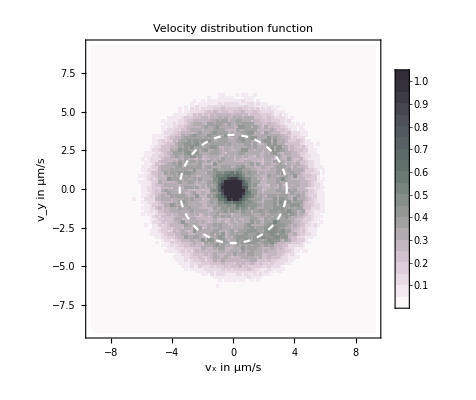

```mathematica
Show[{ListContourPlot[velodistribution,InterpolationOrder->0,PlotRange->All,Contours->Range[0,1,0.05],ColorFunctionScaling->False,ColorFunction->(ColorData[{"PigeonTones","Reverse"}][#]&),PlotLegends->Automatic,FrameLabel->{Style["v_x in μm/s",16],Style["v_y in μm/s",16]},PlotLabel->Style["Velocity distribution function",16]],PolarPlot[3.5,{ϕ,0,2π},PlotStyle->Directive[White,Dashed]]}]
```

```mathematica
orderparameters=Transpose@Table[Abs[Mean[{Exp[I#],Exp[2I#]}&/@(ArcTan[Sequence@@#]&/@DeleteCases[N@Flatten[allvelos[[;;,;;,t]],2],{0.,0.}])]],{t,1,filecount-1}];
```

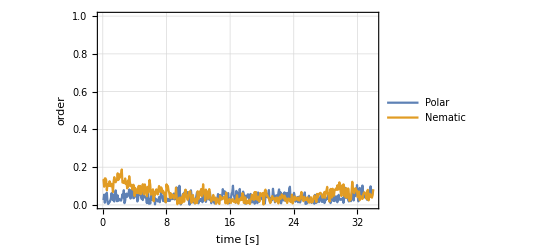

```mathematica
ListLinePlot[{Thread[{Range[filecount-1]*timeunit,orderparameters[[1]]}],Thread[{Range[filecount-1]*timeunit,orderparameters[[2]]}]},Frame->True,GridLines->Automatic,FrameLabel->{"time [s]","order"},PlotLegends->Placed[{"Polar","Nematic"},{0.85,0.5}],PlotRange->{All,{0,1}}]
```